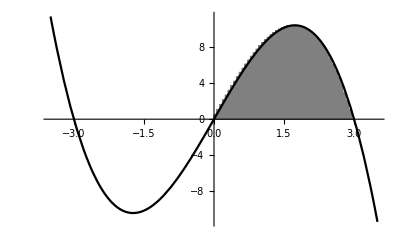

```mathematica
Plot[
9x-x^3,
{x,-3.5,3.5},
PlotStyle->Black,
Prolog->{
Gray,
EdgeForm@Thin,
Table[Rectangle[{(3n-3)/50,0},{3n/50,9(3n/50)-((3n/50)^3)}],{n,1,50}]
}
]
```

```mathematica
Magnify[TableForm[Table[{k,Integrate[Sqrt[x],{x,0,k}]},{k,1,26}],TableHeadings->{None,{"k","integral"}},TableAlignments->Center],1/2]
```

k | integral
1 | 2/3
2 | (4 √2)/3
3 | 2 √3
4 | 16/3
5 | (10 √5)/3
6 | 4 √6
7 | (14 √7)/3
8 | (32 √2)/3
9 | 18
10 | (20 √10)/3
11 | (22 √11)/3
12 | 16 √3
13 | (26 √13)/3
14 | (28 √14)/3
15 | 10 √15
16 | 128/3
17 | (34 √17)/3
18 | 36 √2
19 | (38 √19)/3
20 | (80 √5)/3
21 | 14 √21
22 | (44 √22)/3
23 | (46 √23)/3
24 | 32 √6
25 | 250/3
26 | (52 √26)/3